```mathematica
A = Complement[Range[1, 100], Range[0, 100, 2], Range[0, 100, 3], Range[0, 100, 5]]
Length[A]
```

{1,7,11,13,17,19,23,29,31,37,41,43,47,49,53,59,61,67,71,73,77,79,83,89,91,97}

26

```mathematica
Intersection[Divisors[2010], Divisors[4140]]
```

{1,2,3,5,6,10,15,30}

```mathematica
MatrixRank[{{0,-4,3,3}, {8,1,3,-3},{1,0,0,7},{1,3,4,8}}]
```

4

```mathematica
"Plná hodnost -> jsou LN"
```

```mathematica
Clear[c]
MatrixForm[A = {{a, b}, {c, d}}]
MatrixForm[B = Inverse[A]]
MatrixForm[Simplify[A.B]]
```

(a | b
c | d)

(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

(1 | 0
0 | 1)

```mathematica
ClearAll[pridejSloupec]
pridejSloupec[A_,b_]:=Join[A,Transpose[{b}],2]
```

```mathematica
matice = {{W, X}, {Y, Z}} 
vektor = {1, 2} 
pridejSloupec[matice, vektor]
```

{{W,X},{Y,Z}}

{1,2}

{{W,X,1},{Y,Z,2}}

```mathematica
A = {{1,2,3,1},{1,4,5,2},{2,9,8,3},{5,7,9,2}}
b = {3,2,7,20}
MatrixRank[A]
u = LinearSolve[A, b]
A.u
Reduce[A.{x,y,z,w}==b,{x,y,z,w}]
NullSpace[A]
```

{{1,2,3,1},{1,4,5,2},{2,9,8,3},{5,7,9,2}}

{3,2,7,20}

3

{31/6,2/3,-7/6,0}

{3,2,7,20}

y==2/3&&z==4-x&&w==-31/3+2 x

{{1,0,-1,2}}

```mathematica
"Báze jádra odpovídá koeficientům u parametru"
```

```mathematica
hilbert[n_]:= Table[1/(i+j-1),{i, 1, n}, {j, 1, n}]
```

```mathematica
hilbert[10]
```

{{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10},{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11},{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12},{1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13},{1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14},{1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15},{1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16},{1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17},{1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18},{1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19}}

```mathematica
AbsoluteTiming[Inverse[hilbert[100]];]
```

{0.53197,Null}

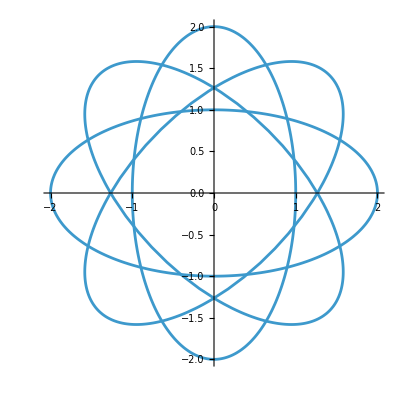

```mathematica
ParametricPlot[Table[{{Cos[k*Pi/4], -Sin[k*Pi/4]},{Sin[k*Pi/4],Cos[k*Pi/4]}}.{2Cos[t],Sin[t]}, {k, 0, 3}],{t, 0, 2Pi}]
```

```mathematica
latinskyCtverec[p_,a_]:=Table[Mod[a*i+j,p],{i, 0, p-1}, {j, 0, p-1}]//MatrixForm
latinskeCtverce[p_]:=Table[latinskyCtverec[p,a], {a, 1, p-1}]
```

```mathematica
latinskeCtverce[7]
```

{(0 | 1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 4 | 5 | 6 | 0
2 | 3 | 4 | 5 | 6 | 0 | 1
3 | 4 | 5 | 6 | 0 | 1 | 2
4 | 5 | 6 | 0 | 1 | 2 | 3
5 | 6 | 0 | 1 | 2 | 3 | 4
6 | 0 | 1 | 2 | 3 | 4 | 5),(0 | 1 | 2 | 3 | 4 | 5 | 6
2 | 3 | 4 | 5 | 6 | 0 | 1
4 | 5 | 6 | 0 | 1 | 2 | 3
6 | 0 | 1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5 | 6 | 0
3 | 4 | 5 | 6 | 0 | 1 | 2
5 | 6 | 0 | 1 | 2 | 3 | 4),(0 | 1 | 2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 0 | 1 | 2
6 | 0 | 1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 6 | 0 | 1
5 | 6 | 0 | 1 | 2 | 3 | 4
1 | 2 | 3 | 4 | 5 | 6 | 0
4 | 5 | 6 | 0 | 1 | 2 | 3),(0 | 1 | 2 | 3 | 4 | 5 | 6
4 | 5 | 6 | 0 | 1 | 2 | 3
1 | 2 | 3 | 4 | 5 | 6 | 0
5 | 6 | 0 | 1 | 2 | 3 | 4
2 | 3 | 4 | 5 | 6 | 0 | 1
6 | 0 | 1 | 2 | 3 | 4 | 5
3 | 4 | 5 | 6 | 0 | 1 | 2),(0 | 1 | 2 | 3 | 4 | 5 | 6
5 | 6 | 0 | 1 | 2 | 3 | 4
3 | 4 | 5 | 6 | 0 | 1 | 2
1 | 2 | 3 | 4 | 5 | 6 | 0
6 | 0 | 1 | 2 | 3 | 4 | 5
4 | 5 | 6 | 0 | 1 | 2 | 3
2 | 3 | 4 | 5 | 6 | 0 | 1),(0 | 1 | 2 | 3 | 4 | 5 | 6
6 | 0 | 1 | 2 | 3 | 4 | 5
5 | 6 | 0 | 1 | 2 | 3 | 4
4 | 5 | 6 | 0 | 1 | 2 | 3
3 | 4 | 5 | 6 | 0 | 1 | 2
2 | 3 | 4 | 5 | 6 | 0 | 1
1 | 2 | 3 | 4 | 5 | 6 | 0)}

```mathematica
rotujiciMatice[seznam_]:= Table[RotateLeft[seznam,i],{i, 0, 9}] //MatrixForm
```

```mathematica
rotujiciMatice[Range[10]]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 1
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 1 | 2
4 | 5 | 6 | 7 | 8 | 9 | 10 | 1 | 2 | 3
5 | 6 | 7 | 8 | 9 | 10 | 1 | 2 | 3 | 4
6 | 7 | 8 | 9 | 10 | 1 | 2 | 3 | 4 | 5
7 | 8 | 9 | 10 | 1 | 2 | 3 | 4 | 5 | 6
8 | 9 | 10 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 10 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9)

```mathematica
MatrixPower[{{1,1},{1,0}},6] //MatrixForm
```

(13 | 8
8 | 5)

```mathematica
"Jsou to členy Fibonacciho posloupnosti"
```